```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/DESI/math

```mathematica
$Assumptions={f>0,V0>0,t>0,x0>0};
```

### Eemeli

```mathematica
u1[t_]=(-Sin[(π t)/T])/Sqrt[U0/ρ-Sin[(π t)/T]^2];
u2[t_]=(-U0/ρ Cos[(π t)/T]+(π t)/T Sin[(π t)/T])/Sqrt[U0/ρ-Sin[(π t)/T]^2];
```

```mathematica
G=Simplify[{{u1[T],u2[T]},{u1'[T],u2'[T]}}/.{U0->ρ Tanh[x0]^2,T->(π Cosh[x0])/Sqrt[2]}]
```

{{0,Tanh[x0]},{√2 Csch[x0],-√2 π Csch[x0]}}

```mathematica
Simplify[Tr[G]/.{U0->ρ Tanh[x0]^2,T->(π Cosh[x0])/Sqrt[2]},{x0>0}]
```

-√2 π Csch[x0]

## H = 0

```mathematica
V[x_]=Tanh[x]^2;
```

```mathematica
dT=π/Sqrt[2(1-Tanh[x0]^2)]//Simplify
xsol[t_]=ArcSinh[Cos[(π t)/dT]/Sqrt[1/Tanh[x0]^2-1]]//Simplify
```

(π Cosh[x0])/(√2)

ArcSinh[Cos[√2 t Sech[x0]] Sinh[x0]]

```mathematica
xsol[0]//Simplify
xsol[dT]//Simplify
xsol'[0]
```

x0

-x0

0

```mathematica
Simplify[xsol''[t]+V'[xsol[t]]]
```

0

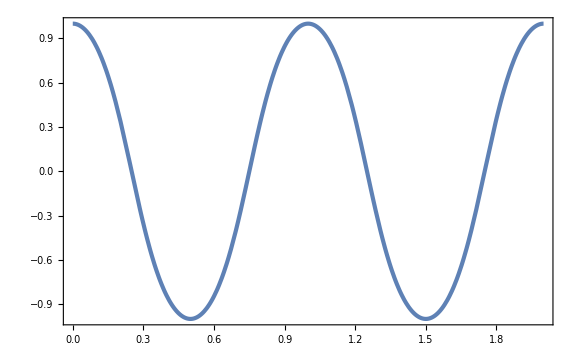

```mathematica
Plot[xsol[tp 2dT]/.{x0->1},{tp,0,2}]
```

```mathematica
V''[x]//Simplify
```

-2 (-2+Cosh[2 x]) Sech[x]^4

```mathematica
FullSimplify[u1''[t]+V''[xsol[t]]u1[t]/.{U0->ρ Tanh[x0]^2,T->(π Cosh[x0])/Sqrt[2]},{x0>0}]
```

(2 (1-2 Cos[√2 t Sech[x0]]^2 Sinh[x0]^2) u1[t])/((1+Cos[√2 t Sech[x0]]^2 Sinh[x0]^2)^2)+u1''[t]

```mathematica
Vpp[t_]=V''[xsol[t]]//Simplify;
```

```mathematica
VppMean=1/dT Integrate[Vpp[t],{t,0,dT}]
```

Sech[x0] (-1+3 Sech[x0]^2)

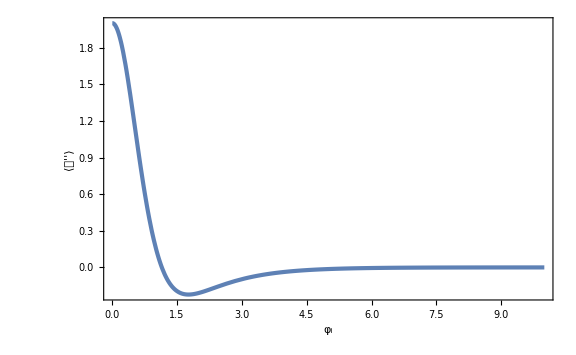

```mathematica
Plot[VppMean,{x0,0,10},PlotRange->Full,FrameLabel->{Subscript[φ, "i"],⟨𝒱''⟩}]
```

```mathematica
Integrate[(Vpp[t]-VppMean),{t,0,dT}]
```

0

```mathematica
VppVar=1/dT Integrate[Vpp[t]^2,{t,0,dT}]-VppMean^2//Simplify
```

1/8 (447+468 Cosh[x0]+92 Cosh[2 x0]+12 Cosh[3 x0]+5 Cosh[4 x0]) Sech[x0]^7 Sinh[x0/2]^4

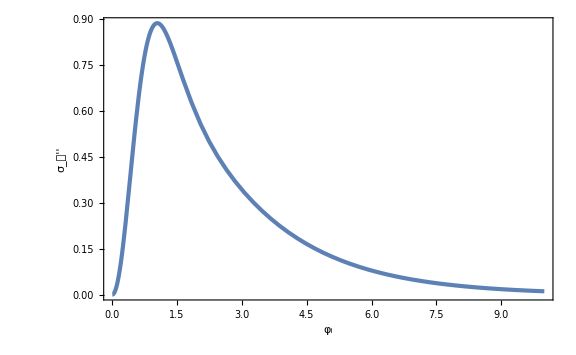

```mathematica
Plot[Sqrt[VppVar],{x0,0,10},FrameLabel->{Subscript[φ, "i"],Subscript[σ, 𝒱'']}]
```

```mathematica
psi[t_]=-(Vpp[t]-VppMean)/Sqrt[2VppVar]//Simplify;
```

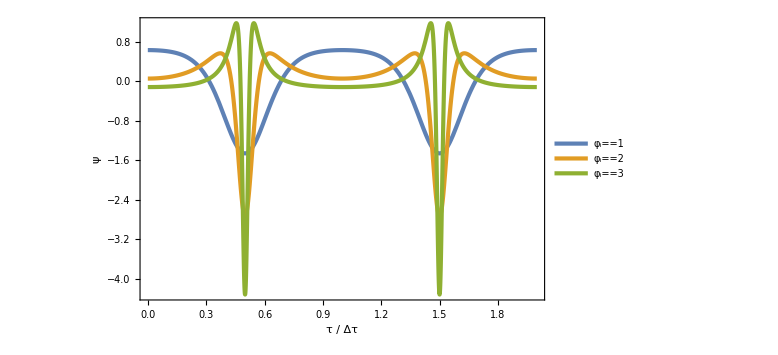

```mathematica
Plot[{psi[tp dT]/.{x0->1},psi[tp dT]/.{x0->2},psi[tp dT]/.{x0->3}},{tp,0,2},PlotRange->Full,FrameLabel->{"τ / Δτ",ψ},PlotLegends->Placed[{Subscript[φ, "i"]==1,Subscript[φ, "i"]==2,Subscript[φ, "i"]==3},{0.5,0.3}]]
```

```mathematica
x0s=1;
FloquetList=Flatten[ParallelTable[u1sol=NDSolve[{u''[t]+(Ak-2q psi[t])u[t]==0,u[0]==1,u'[0]==0}/.{x0->x0s},{u[t],u'[t]},{t,0,dT/.{x0->x0s}}][[1]];
u2sol=NDSolve[{u''[t]+(Ak-2q psi[t])u[t]==0,u[0]==0,u'[0]==1}/.{x0->x0s},{u[t],u'[t]},{t,0,dT/.{x0->x0s}}][[1]];
w[t_]=Transpose[{{u[t],u'[t]}/.u1sol,{u[t],u'[t]}/.u2sol}];
{Ak,q,Re[ArcCosh[1/2 Tr[w[dT]/.{x0->x0s}]]]},{Ak,-0.5,5,10^-2},{q,0,1,10^-2}],1];//AbsoluteTiming
FloquetFig=Show[ListDensityPlot[FloquetList,PlotRange->Full,PlotLegends->BarLegend[Automatic,LegendLabel->Placed["μ_k Δτ",Right]],FrameLabel->{{OverTilde[q],None},{Subscript[A, k],Subscript[φ, "i"]==x0s}},GridLines->{{VppMean/.{x0->x0s}},None},GridLinesStyle->Directive[Color[4],AbsoluteThickness[2]]],Plot[Sqrt[VppVar/2]/.{x0->x0s},{x,-0.5,5},PlotStyle->{Black,Dashed,AbsoluteThickness[3]}]]
Export["Floquet_xi="<>ToString[x0s]<>".pdf",FloquetFig,ImageResolution->300];
```

{10.3291,Null}

-Graphics-

```mathematica
x0s=2;
FloquetList=Flatten[ParallelTable[u1sol=NDSolve[{u''[t]+(Ak-2q psi[t])u[t]==0,u[0]==1,u'[0]==0}/.{x0->x0s},{u[t],u'[t]},{t,0,dT/.{x0->x0s}}][[1]];
u2sol=NDSolve[{u''[t]+(Ak-2q psi[t])u[t]==0,u[0]==0,u'[0]==1}/.{x0->x0s},{u[t],u'[t]},{t,0,dT/.{x0->x0s}}][[1]];
w[t_]=Transpose[{{u[t],u'[t]}/.u1sol,{u[t],u'[t]}/.u2sol}];
{Ak,q,Re[ArcCosh[1/2 Tr[w[dT]/.{x0->x0s}]]]},{Ak,-0.5,5,10^-2},{q,0,1,10^-2}],1];//AbsoluteTiming
FloquetFig=Show[ListDensityPlot[FloquetList,PlotRange->Full,PlotLegends->BarLegend[Automatic,LegendLabel->Placed["μ_k Δτ",Right]],FrameLabel->{{OverTilde[q],None},{Subscript[A, k],Subscript[φ, "i"]==x0s}},GridLines->{{VppMean/.{x0->x0s}},None},GridLinesStyle->Directive[Color[4],AbsoluteThickness[2]]],Plot[Sqrt[VppVar/2]/.{x0->x0s},{x,-0.5,5},PlotStyle->{Black,Dashed,AbsoluteThickness[3]}]]
Export["Floquet_xi="<>ToString[x0s]<>".pdf",FloquetFig,ImageResolution->300];
```

{12.5983,Null}

-Graphics-

```mathematica
x0s=3;
FloquetList=Flatten[ParallelTable[u1sol=NDSolve[{u''[t]+(Ak-2q psi[t])u[t]==0,u[0]==1,u'[0]==0}/.{x0->x0s},{u[t],u'[t]},{t,0,dT/.{x0->x0s}}][[1]];
u2sol=NDSolve[{u''[t]+(Ak-2q psi[t])u[t]==0,u[0]==0,u'[0]==1}/.{x0->x0s},{u[t],u'[t]},{t,0,dT/.{x0->x0s}}][[1]];
w[t_]=Transpose[{{u[t],u'[t]}/.u1sol,{u[t],u'[t]}/.u2sol}];
{Ak,q,Re[ArcCosh[1/2 Tr[w[dT]/.{x0->x0s}]]]},{Ak,-0.5,5,10^-2},{q,0,1,10^-2}],1];//AbsoluteTiming
FloquetFig=Show[ListDensityPlot[FloquetList,PlotRange->Full,PlotLegends->BarLegend[Automatic,LegendLabel->Placed["μ_k Δτ",Right]],FrameLabel->{{OverTilde[q],None},{Subscript[A, k],Subscript[φ, "i"]==x0s}},GridLines->{{VppMean/.{x0->x0s}},None},GridLinesStyle->Directive[Color[4],AbsoluteThickness[2]]],Plot[Sqrt[VppVar/2]/.{x0->x0s},{x,-0.5,5},PlotStyle->{Black,Dashed,AbsoluteThickness[3]}]]
Export["Floquet_xi="<>ToString[x0s]<>".pdf",FloquetFig,ImageResolution->300];
```

{13.4266,Null}

-Graphics-

```mathematica
FloquetFunc=Flatten[ParallelTable[u1sol=NDSolve[{u''[t]+(Ak-2q psi[t])u[t]==0,u[0]==1,u'[0]==0}/.{Ak->k^2+VppMean,q->Sqrt[VppVar/2]},{u[t],u'[t]},{t,0,dT}][[1]];
u2sol=NDSolve[{u''[t]+(Ak-2q psi[t])u[t]==0,u[0]==0,u'[0]==1}/.{Ak->k^2+VppMean,q->Sqrt[VppVar/2]},{u[t],u'[t]},{t,0,dT}][[1]];
w[t_]=Transpose[{{u[t],u'[t]}/.u1sol,{u[t],u'[t]}/.u2sol}];
{k,x0,Re[ArcCosh[1/2 Tr[w[dT]/.{x0->x0s}]]]},{x0,1,3,10^-2},{k,0,3,10^-2}],1];//AbsoluteTiming
```

{14.1996,Null}

```mathematica
FloquetFuncFig=ListDensityPlot[FloquetFunc,FrameLabel->{k,Subscript[φ, "i"]},PlotLegends->BarLegend[Automatic,LegendLabel->Placed["μ_k Δτ",Right]],PlotRange->Full]
```

-Graphics-

```mathematica
Export["Floquet.pdf",FloquetFuncFig,ImageResolution->300];
```

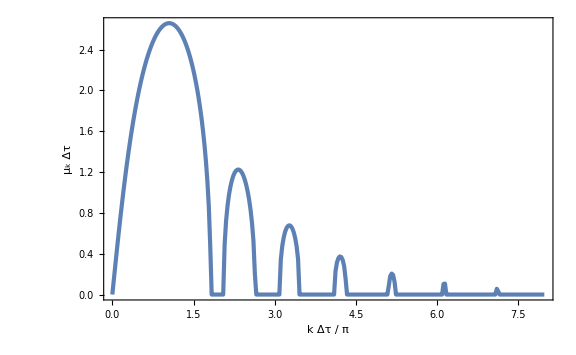

```mathematica
ListPlot[Map[{#[[1]]dT/π/.{x0->2},#[[3]]}&,Select[FloquetFunc,#[[2]]==2&]],PlotRange->Full,FrameLabel->{{Row[{Subscript[μ, k]," ",Δτ}],None},{Row[{k Δτ," / ",π}],Subscript[φ, "i"]==2}}]
```

## w/ matter

```mathematica
f=10^-3;
h=0.66;(*0.674;*)
Ωm=0.32(*0.3;*)
ρm0=3 h^2 Ωm;
V0=1.1 3(1-Ωm)h^2;
xi=7.35f;
zi=9;(*1000;*)
mth=Sqrt[V0]/f
```

0.32

988.679

```mathematica
V[x_]=V0 Tanh[x/f]^2;
H[x_,p_,z_]=Sqrt[(p^2/2+V[x]+ρm0(1+z)^3)/3];
```

```mathematica
Hi=H[xi,0,zi];
tf=20/Hi;
```

```mathematica
txmax={};
txzero={};
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t],z[t]]x'[t]+V'[x[t]]==0,z'[t]==-(1+z[t])H[x[t],x'[t],z[t]],x[0]==xi,x'[0]==0,z[0]==zi,WhenEvent[x'[t]==0,AppendTo[txmax,t]],WhenEvent[x[t]==0,AppendTo[txzero,t]],WhenEvent[z[t]==0,t0=t]},{x[t],x'[t],z[t]},{t,0,tf},WorkingPrecision->30,MaxSteps->10^5][[1]];
```

NDSolve::precw: The precision of the differential equation ({{1954.97 Sech[Times[«2»]]^2 Tanh[1000 x[«1»]]+√3 x'[t] √(Times[«2»]+Times[«2»]+Times[«2»])+x''[t]==0,z'[t]==((-1-z[t]) √(0.977486 Power[«2»]+0.418176 Power[«2»]+1/2 Power[«2»]))/(√3),x[0]==0.00735,x'[0]==0,z[0]==9},{},{},{},{WhenEvent[x'[t]==0,AppendTo[txmax,t]],WhenEvent[x[t]==0,AppendTo[txzero,t]],WhenEvent[z[t]==0,t0=t]}}) is less than WorkingPrecision (30.).

```mathematica
xsol[t_]=x[t]/.bgsol;
psol[t_]=x'[t]/.bgsol;
zsol[t_]=z[t]/.bgsol;
Hsol[t_]=H[xsol[t],psol[t],zsol[t]];
wsol[t_]=(psol[t]^2/2-V[xsol[t]])/(psol[t]^2/2+V[xsol[t]]);
Vppsol[t_]=V''[xsol[t]];
dTList=Differences[txmax];
```

```mathematica
VppMeanList=ParallelTable[1/dTList[[i]] NIntegrate[Vppsol[t]/mth^2,{t,txmax[[i]],txmax[[i+1]]}],{i,Length[dTList]}];//AbsoluteTiming
```

{69.826,Null}

```mathematica
VppVarList=ParallelTable[1/dTList[[i]] NIntegrate[Vppsol[t]^2/mth^4,{t,txmax[[i]],txmax[[i+1]]}]-VppMeanList[[i]]^2,{i,Length[dTList]}];//AbsoluteTiming
```

{42.2526,Null}

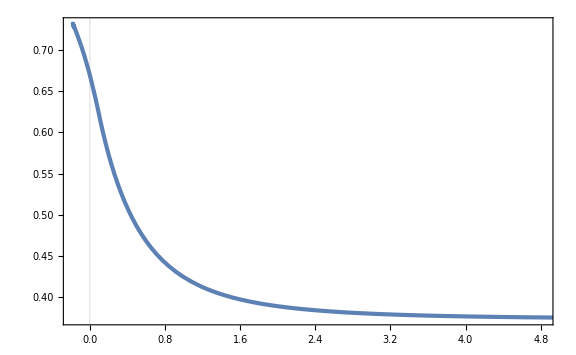

```mathematica
ParametricPlot[{zsol[t],(1+zsol[t])^(-3/2)Hsol[t]},{t,0,tf},GridLines->{{0},None}]
```

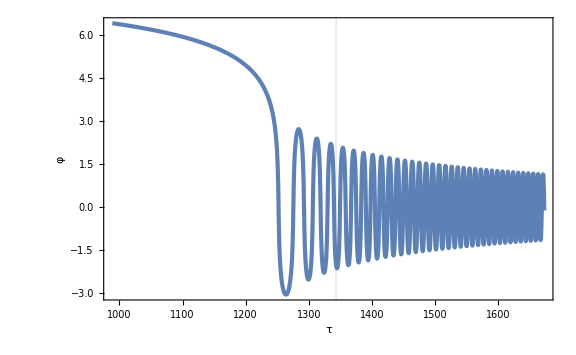

```mathematica
Plot[xsol[tp/mth]/f,{tp,mth,tf mth},PlotRange->Full,GridLines->{{mth t0},None},FrameLabel->{τ,φ}]
```

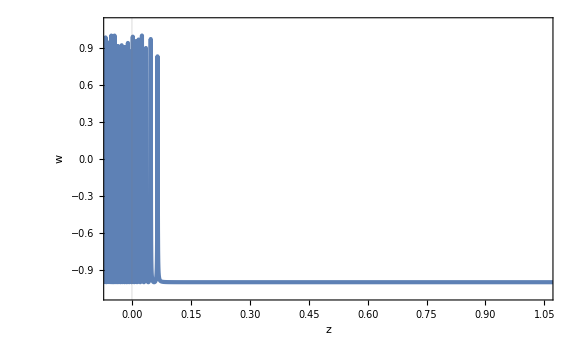

```mathematica
ParametricPlot[{zsol[t],wsol[t]},{t,0,tf},PlotRange->{{-0.05,1.05},{-1.1,1.1}},FrameLabel->{z,w},GridLines->{{0},None}]
```

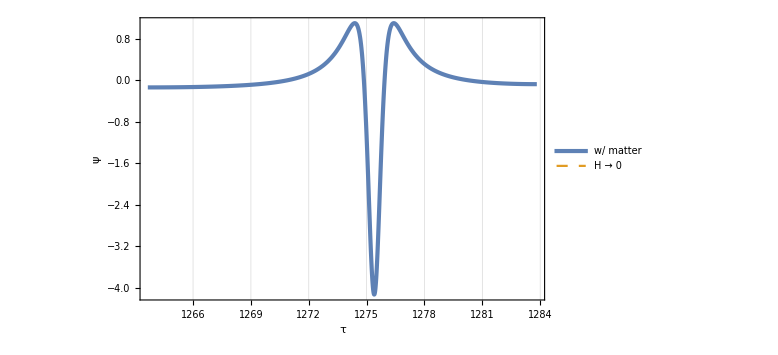

```mathematica
is=1;
Plot[{-(Vppsol[tp/mth]/mth^2-VppMeanList[[is]])/Sqrt[2VppVarList[[is]]],psi[tp-mth txzero[[is+1]]+1/2 dT]/.{x0->(Abs[xsol[txmax[[is]]]]+Abs[xsol[txmax[[is+1]]]])/(2f)}},{tp,mth txmax[[is]],mth txmax[[is+1]]},PlotRange->Full,GridLines->{txzero,None},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{ψ,None},{τ,"Oscillation "<>ToString[is]}},PlotLegends->Placed[{"w/ matter","H → 0"},{0.2,0.2}]]
```

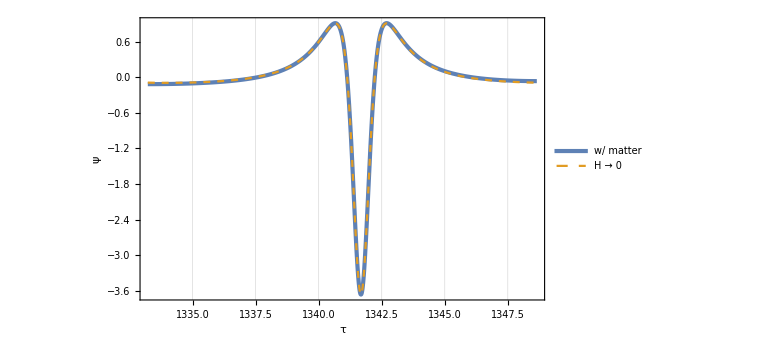

```mathematica
is=2;
Plot[{-(Vppsol[tp/mth]/mth^2-VppMeanList[[is]])/Sqrt[2VppVarList[[is]]],psi[tp-mth txzero[[is+1]]+1/2 dT]/.{x0->(Abs[xsol[txmax[[is]]]]+Abs[xsol[txmax[[is+1]]]])/(2f)}},{tp,mth txmax[[is]],mth txmax[[is+1]]},PlotRange->Full,GridLines->{txzero,None},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{ψ,None},{τ,"Oscillation "<>ToString[is]}},PlotLegends->Placed[{"w/ matter","H → 0"},{0.2,0.2}]]
```

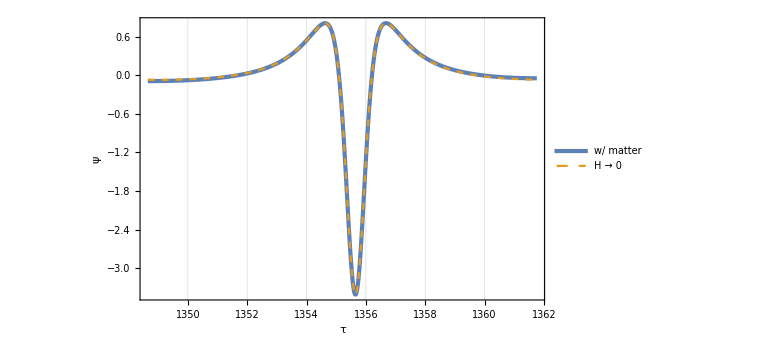

```mathematica
is=3;
Plot[{-(Vppsol[tp/mth]/mth^2-VppMeanList[[is]])/Sqrt[2VppVarList[[is]]],psi[tp-mth txzero[[is+1]]+1/2 dT]/.{x0->(Abs[xsol[txmax[[is]]]]+Abs[xsol[txmax[[is+1]]]])/(2f)}},{tp,mth txmax[[is]],mth txmax[[is+1]]},PlotRange->Full,GridLines->{txzero,None},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{ψ,None},{τ,"Oscillation "<>ToString[is]}},PlotLegends->Placed[{"w/ matter","H → 0"},{0.2,0.2}]]
```

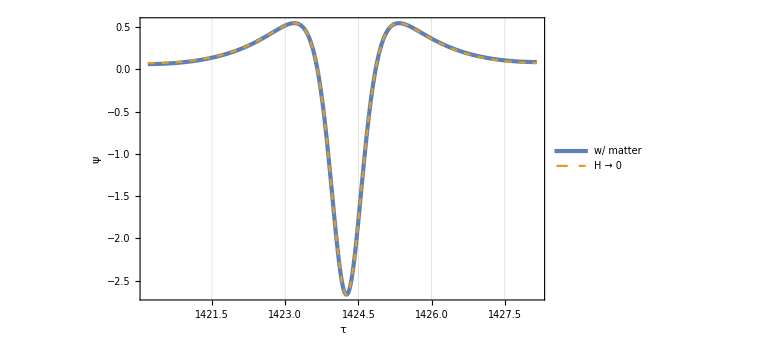

```mathematica
is=10;
Plot[{-(Vppsol[tp/mth]/mth^2-VppMeanList[[is]])/Sqrt[2VppVarList[[is]]],psi[tp-mth txzero[[is+1]]+1/2 dT]/.{x0->(Abs[xsol[txmax[[is]]]]+Abs[xsol[txmax[[is+1]]]])/(2f)}},{tp,mth txmax[[is]],mth txmax[[is+1]]},PlotRange->Full,GridLines->{txzero,None},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{ψ,None},{τ,"Oscillation "<>ToString[is]}},PlotLegends->Placed[{"w/ matter","H → 0"},{0.2,0.2}]]
```

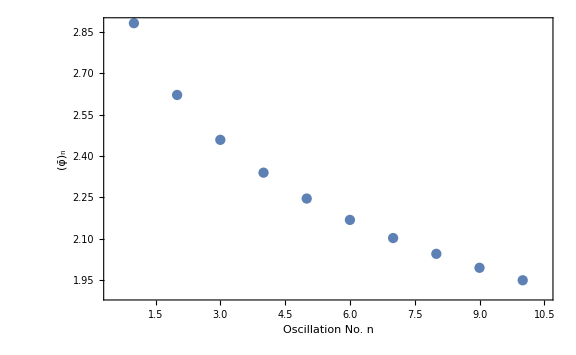

```mathematica
ListPlot[Table[{i,(Abs[xsol[txmax[[i]]]]+Abs[xsol[txmax[[i+1]]]])/(2f)},{i,1,10}],Joined->False,PlotRange->{{0.5,10.5},Full},FrameLabel->{"Oscillation No. n",Subscript[OverBar[φ], n]}]
```

```mathematica
((1+zsol[txmax[[1]]])/(1+zsol[txmax[[1+1]]]))^(3/2)
```

1.02151

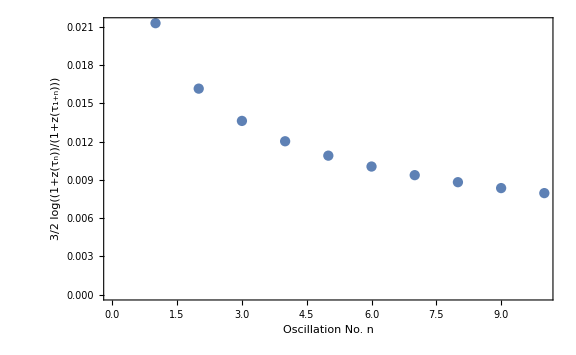

```mathematica
ListPlot[Table[{i,Log[((1+zsol[txmax[[i]]])/(1+zsol[txmax[[i+1]]]))^(3/2)]},{i,1,10}],Joined->False,FrameLabel->{"Oscillation No. n",3/2 Log[(1+z[Subscript[τ, n]])/(1+z[Subscript[τ, n+1]])]}]
```

```mathematica
mth dTList[[1]]
(Abs[xsol[txmax[[1]]]]+Abs[xsol[txmax[[2]]]])/(2f)
dT/.{x0->(Abs[xsol[txmax[[1]]]]+Abs[xsol[txmax[[2]]]])/(2f)}
((dT/.{x0->xsol[txmax[[1]]]/f})+(dT/.{x0->xsol[txmax[[2]]]/f}))/2
```

20.1483

2.88084

19.8656

20.1348

```mathematica
dT
```

(π Cosh[x0])/(√2)

### perturbation

```mathematica
ti=0(*t/.FindRoot[zsol[t]==9,{t,t0/100},WorkingPrecision->30]*)
```

0

```mathematica
ks=10^-3;
ptbsol=NDSolve[{dx''[t]+3Hsol[t]dx'[t]+(k^2 mth^2(1+zsol[t])^2+Vppsol[t])dx[t]==0,
dx[ti]==(1+zsol[ti])/Sqrt[2k mth],dx'[ti]==-I k mth(1+zsol[ti])dx[ti]}/.{k->ks},dx[t],{t,ti,t0},WorkingPrecision->30,MaxSteps->10^5][[1]];
```

NDSolve::precw: The precision of the differential equation ({{dx[t] (1.95497 Power[10, 6] Power[<<2>>] + <<2>>) + <<2>> == 0, <<2>>}, {}, <<2>>, {}}) is less than WorkingPrecision (30.).

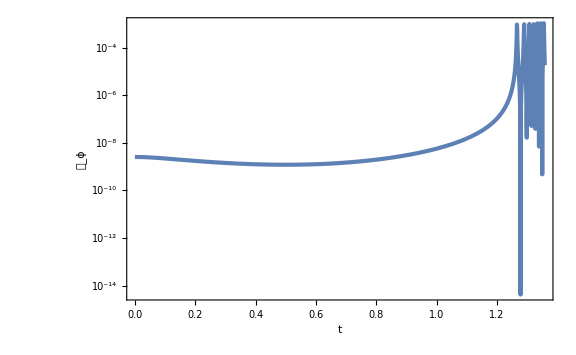

```mathematica
LogPlot[ks^3/(2 π^2)Abs[dx[t]]^2/.ptbsol,{t,ti,t0},PlotRange->Full,FrameLabel->{{Subscript[𝒫, ϕ],None},{t,k==10^-3}}]
```

```mathematica
ptbsolList[t_]=ParallelTable[k=10^lnk;{k,dx[t]/.NDSolve[{dx''[t]+3Hsol[t]dx'[t]+(k^2 mth^2(1+zsol[t])^2+Vppsol[t])dx[t]==0,
dx[ti]==(1+zsol[ti])/Sqrt[2k mth],dx'[ti]==-I k mth(1+zsol[ti])dx[ti]},dx[t],{t,ti,t0},WorkingPrecision->30,MaxSteps->10^5][[1]]//Quiet},{lnk,-4,0,10^-2}];//AbsoluteTiming
```

{794.59,Null}

```mathematica
calPList[t_]=Map[{#[[1]],(#[[1]])^3/(2 π^2)Abs[#[[2]]]^2}&,ptbsolList[t]];
```

```mathematica
dt=20/660;
Nt=Floor[(t0-ti)/dt]
```

44

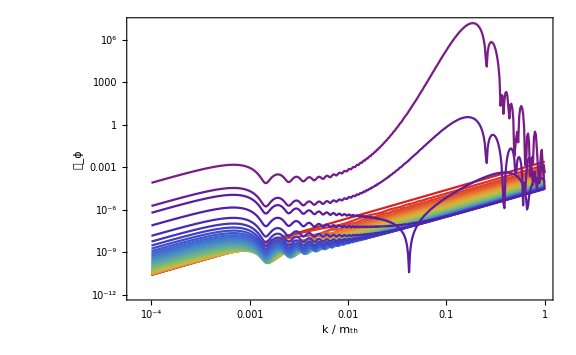

```mathematica
(*dt=10/mth;*)
(*Nt=15;*)
ListLogLogPlot[Table[calPList[t],{t,(*t0-Nt dt*)ti,t0,dt}],FrameLabel->{{Subscript[𝒫, ϕ],None},{"k / m_th","t = 20 / (660H_*)"(*"Δt = 10 / m_th"*)}},PlotStyle->Table[ColorData["Rainbow"][1-i/Nt],{i,0,Nt}]]
```

```mathematica
2 10^(-33-9)1000//N
```

2.×10^-39

```mathematica
1/(4 π^2)//N
```

0.0253303